# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :

# Grafos

## Práctica 4

### Código

```mathematica
(*Matriz de adyacencia*)
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];

.08(*Matriz de incidencia*)
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];

(*Grado*)
GRADO[n_,F_]:=Module[{i},
grado=0;
Do[If[Intersection[{F[[i]][[1]],F[[i]][[2]]},{n}]=={n},grado++],{i,Length[F]}];
grado
]
(*Regular*)
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
REGULAR2[W_,F_]:=Module[{i,j},
grado=GRADO[W[[1]],F];
regular=True;
Do[
If[grado≠GRADO[W[[i]],F],regular=False];
,{i,2,Length[W]}];
If[regular,Print["El grafo es ",grado,"-regular"],Print["El grafo no es regular"];]
];
(*Completo*)
COMPLETO[matrizadyacencia_]:=
(Sum[MatrixPower[matrizadyacencia,2][[i,i]],
{i,Dimensions[matrizadyacencia][[1]]}]==
Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))

(*Isomorfos*)
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   
Do[	      
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
```

.08

```mathematica
(*Bipartito*)
IND[W1_,F_]:=Module[{i},
F1={};
Do[If[Sort[Intersection[{F[[i]][[1]],F[[i]][[2]]},W1]]==Sort[{F[[i]][[1]],F[[i]][[2]]}],AppendTo[F1,F[[i]]]],{i,Length[F]}];
F1
]
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
bipartito=False;
i=1;
fin=Quotient[Length[W],2];
While[!bipartito && i<=fin,
subconjuntos=KSubsets[W,i];
j=1;
While[!bipartito && j<=Length[subconjuntos],
If[IND[subconjuntos[[j]],F]=={},
If[IND[Complement[W,subconjuntos[[j]]],F]=={},
bipartito=True;
W1=subconjuntos[[j]];
W2=Complement[W,subconjuntos[[j]]];
];
];
j++;];
i++;];
If[bipartito,Print["Es bipartito: W1=",W1," y W2=",W2];
If[Length[F]==Length[W1]*Length[W2],Print["Es bipartito completo: ",Subscript["K", Length[W1],Length[W2]]  ], Print["No es bipartito completo"]];
,Print["No es bipartito"]];
]
```

### Ejercicio 5.29 Grafos I

a) Sea W el conjunto formado por todas las cifras distintas que componen su DNI junto con todas las letras distintas de su primer apellido.
b) Consideramos el grafo no orientado G_1 cuyo conjunto de vértices es W y donde dos vértices cuales quiera serán adyacentes si y sólo si son:
	I. Un número par y una vocal
	II. Un número impar y una consonante
	III. Dos números pares distintos
c) Consideramos el grafo dirigido G_2 cuyo conjunto de vértices es W y donde el conjunto de flechas está formado por todas aquellas flechas que podemos considerar de la forma:
	I. Origen en un número impar y fin de una vocal 
	II. Origen en una vocal y fin en una constante 
	III. Origen en un número par y fin en un número impar
Se pide:
	i. Definir G_1 y G_2 directamente por sus conjuntos de vértices y lados o flechas

```mathematica
W={2,6,8,0,,"m","a","r","t","i","n","l","u","s"}; (*Comparten vértices ambos grafos*)
(*ARISTAS PRIMER GRAFO:par a vocal y pares distintos*)
F1={ 
	{0,"a"},{0,"i"},{0,"u"},
	{2,"a"},{2,"i"},{2,"u"},
	{6,"a"},{6,"i"},{6,"u"},
	{8,"a"},{8,"i"},{8,"u"},
	{2,6},{2,8},{2,6}
	};
(*ARISTAS SEGUNDO GRAFO: impar a vocal , vocal a consonante y par a impar *)
F2={
	{"a","m"},{"a","r"},{"a","t"},{"a","n"},{"a","l"},{"a","s"},
	{"i","m"},{"i","r"},{"i","t"},{"i","n"},{"i","l"},{"i","s"},
	{"u","m"},{"u","r"},{"u","t"},{"u","n"},{"u","l"},{"u","s"}
	};
```

ii. Calcular las matrices de adyacencia de G_1 y G_2

```mathematica
"G1"
A1=MATRIZADYACENCIA[W,F1];
A1//MatrixForm
"G2"
A2=MATRIZADYACENCIA[W,F2];
A2//MatrixForm
```

G1

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

G2

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

iii. Calcular la matriz de incidencia de G_1

```mathematica
"G1"
I1=MATRIZINCIDENCIA[W,F1];
I1//MatrixForm
```

G1

(0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

iv. Representar gráficamente G_1 y G_2

```mathematica
GraphPlot[A1,DirectedEdges->True]
```

-Graphics-

```mathematica
GraphPlot[A2,DirectedEdges->True]
```

-Graphics-

### Ejercicio 2 Grafos I

Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

a)

```mathematica
WEjer2GIa={1,2,3,4,5,6};
FEjer2GIa={1->2,3->1,4->5,6->1}

"MATRIZADYACENCIA"
AEjer2GIa=MATRIZADYACENCIA[WEjer2GIa,FEjer2GIa];
AEjer2GIa//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIa=MATRIZINCIDENCIA[WEjer2GIa,FEjer2GIa];
IEjer2GIa//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIa;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIa,DirectedEdges->True]
```

{1→2,3→1,4→5,6→1}

MATRIZADYACENCIA

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

MATRIZINCIDENCIA

(1 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6}

{2→1,3→1,6→1,1→2,1→3,5→4,4→5,1→6}

Representacion gráfica

-Graphics-

b)

```mathematica
matrizadyacenciaEjer2GIb=({{0, 1, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}});
W=Table[i,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}]
F={};
Do[Do[If[matrizadyacenciaEjer2GIb[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];,{j,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];
F
```

{1,2,3,4}

{2→1,4→1,1→2,3→2,2→3,4→3,1→4,3→4}

```mathematica
WEjer2GIb={1,2,3,4};
FEjer2GIb={2->1,4->1,1->2,3->2,2->3,4->3,1->4,3->4};
"MATRIZINCIDENCIA"
IEjer2GIb=MATRIZINCIDENCIA[WEjer2GIb,FEjer2GIb];
IEjer2GIb//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}]
F={};
Do[Do[If[matrizadyacenciaEjer2GIb[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];,{j,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];
F
"Representacion gráfica"
GraphPlot[matrizadyacenciaEjer2GIb,DirectedEdges->True]
```

MATRIZINCIDENCIA

(1 | 1 | 1 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 1 | 1)

Vertices y lados

{1,2,3,4}

{2→1,4→1,1→2,3→2,2→3,4→3,1→4,3→4}

Representacion gráfica

-Graphics-

c)

```mathematica
matrizincidenciaEjer2GIc=({{1, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}});

W=Table[i,{i,Dimensions[matrizincidenciaEjer2GIc][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer2GIc][[2]]}];
F
```

{1,2,3,4,5}

{1→4,1→5,2→4,2→5,3→4,3→5}

```mathematica
WEjer2GIc={1,2,3,4,5};
FEjer2GIc={1->4,1->5,2->4,2->5,3->4,3->5};
"MATRIZADYACENCIA"
AEjer2GIc=MATRIZADYACENCIA[WEjer2GIc,FEjer2GIc];
AEjer2GIc//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[AEjer2GIc][[1]]}]
F={};
Do[Do[If[AEjer2GIc[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[AEjer2GIc][[1]]}];,{j,Dimensions[AEjer2GIc][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIc,DirectedEdges->True]
```

MATRIZADYACENCIA

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

Vertices y lados

{1,2,3,4,5}

{4→1,5→1,4→2,5→2,4→3,5→3,1→4,2→4,3→4,1→5,2→5,3→5}

Representacion gráfica

-Graphics-

d)

```mathematica
"d"
WEjer2GIdg4={1,2,3,4,5,6,7,8};
FEjer2GIdg4={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8}
"MATRIZADYACENCIA"
AEjer2GIdg4=MATRIZADYACENCIA[WEjer2GIdg4,FEjer2GIdg4];
AEjer2GIdg4//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg4=MATRIZINCIDENCIA[WEjer2GIdg4,FEjer2GIdg4];
IEjer2GIdg4//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIdg4;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIdg4,DirectedEdges->True]
```

d

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→1,1→4,2→7,3→6,5→8}

MATRIZADYACENCIA

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

MATRIZINCIDENCIA

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6,7,8}

{2→1,4→1,8→1,1→2,3→2,7→2,2→3,4→3,6→3,1→4,3→4,5→4,4→5,6→5,8→5,3→6,5→6,7→6,2→7,6→7,8→7,1→8,5→8,7→8}

Representacion gráfica

-Graphics-

```mathematica
WEjer2GIdg5={1,2,3,4};
FEjer2GIdg5={1->2,2->3,3->1,1->4,2->4,3->4}
"MATRIZADYACENCIA"
AEjer2GIdg5=MATRIZADYACENCIA[WEjer2GIdg5,FEjer2GIdg5];
AEjer2GIdg5//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg5=MATRIZINCIDENCIA[WEjer2GIdg5,FEjer2GIdg5];
IEjer2GIdg//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIdg5;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"Representacion gráfica"
GraphPlot[AEjer2GIdg5,DirectedEdges->True]
```

{1→2,2→3,3→1,1→4,2→4,3→4}

MATRIZADYACENCIA

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

MATRIZINCIDENCIA

IEjer2GIdg

Vertices y lados

{1,2,3,4}

{2→1,3→1,4→1,1→2,3→2,4→2,1→3,2→3,4→3,1→4,2→4,3→4}

Representacion gráfica

-Graphics-

### Ejercicio 3 Grafos I

Ejercicio 5.4 del manual de prácticas
Sacar

```mathematica
matrizincidenciaEjer3GIc=({{1, 0, 0, 1, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 1, 0, 0, 1}, {0, 1, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 1}});


W=Table[i,{i,Dimensions[matrizincidenciaEjer3GIc][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer3GIc][[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer3GIc][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer3GIc][[2]]}];
F
```

{1,2,3,4,5,6}

{1→6,2→5,3→4,1→2,3→5,4→6}

```mathematica
"G1";
WEjer3GIdg1={1,2,3,4,5,6};
FEjer3GIdg1={{1,2},{2,3},{3,6},{6,5},{5,4},{4,2}};
"G3";
WEjer3GIdg3={1,2,3,4,5,6};
FEjer3GIdg3={{1,6},{1,5},{2,4},{2,6},{3,4},{3,5}};
"G5";
WEjer3GIdg5={1,2,3,4,5,6};
FEjer3GIdg5={1->6,2->5,3->4,1->2,3->5,4->6};
"G6";
WEjer3GIdg6={1,2,3,4,5,6};
FEjer3GIdg6={1->2, 1->3, 2->3, 3->5, 4->5,4->6, 5->6};
```

```mathematica
"G1"
AG1=MATRIZADYACENCIA[WEjer3GIdg1,FEjer3GIdg1];
MatrixForm[AG1]
"G2"
AG2=({{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0}})
"G3"
AG3=MATRIZADYACENCIA[WEjer3GIdg3,FEjer3GIdg3];
MatrixForm[AG3]
"G4"
AG4=({{0, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 1}, {0, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 1, 0, 0, 1, 0}})
"G5"
AG5=MATRIZADYACENCIA[WEjer3GIdg5,FEjer3GIdg5];
MatrixForm[AG5]
"G6"
AG6=MATRIZADYACENCIA[WEjer3GIdg6,FEjer3GIdg6];
MatrixForm[AG6]
```

G1

(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0)

G2

{{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}}

G3

(0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0)

G4

{{0,1,0,0,0,1},{1,0,0,0,0,1},{0,0,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,1,0,0,1,0}}

G5

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0)

G6

(0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0)

```mathematica
"G1 y G2"
ISOMORFOS[AG1,AG2]
"G1 y G3"
ISOMORFOS[AG1,AG3]
"G1 y G4"
ISOMORFOS[AG1,AG4]
"G1 y G5"
ISOMORFOS[AG1,AG5]
"G1 y G6"
ISOMORFOS[AG1,AG6]
"G2 y G3"
ISOMORFOS[AG2,AG3]
"G2 y G4"
ISOMORFOS[AG2,AG4]
"G2 y G5"
ISOMORFOS[AG2,AG5]
"G2 y G6"
ISOMORFOS[AG2,AG6]
"G3 y G4"
ISOMORFOS[AG3,AG4]
"G3 y G5"
ISOMORFOS[AG3,AG5]
"G3 y G6"
ISOMORFOS[AG3,AG6]
"G4 y G5"
ISOMORFOS[AG4,AG5]
"G4 y G6"
ISOMORFOS[AG4,AG6]
"G5 y G6"
ISOMORFOS[AG5,AG6]
```

G1 y G2

No son isomorfos

G1 y G3

No son isomorfos

G1 y G4

No son isomorfos

G1 y G5

No son isomorfos

G1 y G6

No son isomorfos

G2 y G3

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 3 | 5 | 4 | 6 | 2)

G2 y G4

No son isomorfos

G2 y G5

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 4 | 5 | 3 | 6)

G2 y G6

No son isomorfos

G3 y G4

No son isomorfos

G3 y G5

Son isomorfos, una matriz P es: (1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1), una permutación es: (1 | 2 | 3 | 4 | 5 | 6
1 | 5 | 4 | 2 | 3 | 6)

G3 y G6

No son isomorfos

G4 y G5

No son isomorfos

G4 y G6

No son isomorfos

G5 y G6

No son isomorfos

### Ejercicio 1: Grafos II

Determinar cuáles de los siguientes grafos son regulares, completos, bipartitos o bipartitos completos.

a)

```mathematica
WEjer2GIIa={1,2,3,4,5,6};
FEjer2GIIa={{1,2},{3,1},{4,5},{6,1}};
AEjer2GIIa=MATRIZADYACENCIA[WEjer2GIIa,FEjer2GIIa];
MatrixForm[AEjer2GIIa]
REGULAR2[WEjer2GIIa,FEjer2GIIa]
COMPLETO[AEjer2GIIa]
BIPARTITO[WEjer2GIIa,FEjer2GIIa]
```

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

El grafo no es regular

False

Es bipartito: W1=1 y W2=Complement[{1,2,3,4,5,6},1]

No es bipartito completo

```mathematica
WEjer2GIIG2={1,2,3,4};
FEjer2GIIG2={1->2,2->3,1->4,3->4}
AEjer2GII2a=MATRIZADYACENCIA[WEjer2GIIG2,FEjer2GIIG2];
MatrixForm[AEjer2GII2a]
REGULAR2[WEjer2GIIG2,FEjer2GIIG2]
COMPLETO[AEjer2GII2a]
BIPARTITO[WEjer2GIIG2,FEjer2GIIG2]
```

{1→2,2→3,1→4,3→4}

(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

El grafo es 2-regular

False

Es bipartito: W1=1 y W2=Complement[{1,2,3,4},1]

No es bipartito completo

```mathematica
WEjer2GIIG3={1,2,3,4,5};
FEjer2GIIG3={1->4,1->5,2->4,2->5,3->4,2->5};
AEjer2GII3a=MATRIZADYACENCIA[WEjer2GIIG3,FEjer2GIIG3];
MatrixForm[AEjer2GII3a]
REGULAR2[WEjer2GIIG3,FEjer2GIIG3]
COMPLETO[AEjer2GII3a]
BIPARTITO[WEjer2GIIG3,FEjer2GIIG3]
```

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)

El grafo no es regular

False

Es bipartito: W1=1 y W2=Complement[{1,2,3,4,5},1]

No es bipartito completo

```mathematica
WEjer2GIIG4={1,2,3,4,5,6,7,8};
FEjer2GIIG4={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{1,4},{2,7},{3,6},{5,8}};
AEjer2GII4a=MATRIZADYACENCIA[WEjer2GIIG4,FEjer2GIIG4];
MatrixForm[AEjer2GII4a]
REGULAR2[WEjer2GIIG4,FEjer2GIIG4]
COMPLETO[AEjer2GII4a]
BIPARTITO[WEjer2GIIG4,FEjer2GIIG4]
```

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

El grafo no es regular

False

Es bipartito: W1=1 y W2=Complement[{1,2,3,4,5,6,7,8},1]

No es bipartito completo

```mathematica
WEjer2GIIG5={1,2,3,4};
FEjer2GIIG5={{1,2},{2,3},{3,1},{1,4},{2,4},{3,4}};
AEjer2GII5a=MATRIZADYACENCIA[WEjer2GIIG5,FEjer2GIIG5];
MatrixForm[AEjer2GII5a]
REGULAR2[WEjer2GIIG5,FEjer2GIIG5]
COMPLETO[AEjer2GII5a]
BIPARTITO[WEjer2GIIG5,FEjer2GIIG5]
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

El grafo es 3-regular

True

Es bipartito: W1=1 y W2=Complement[{1,2,3,4},1]

No es bipartito completo

### Ejercicio 2: Grafos II

Estudiar si el grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24, es
regular, completo, bipartito y/o bipartito completo. Análogamente para un decágono.

```mathematica
WEjer2GII={1,2,3,4,5,6};
FEjer2GII={1->2,2->3,3->4,4->5,5->6,6->1,1->4,2->5,3->6};
AEjer2GII=MATRIZADYACENCIA[WEjer2GII,FEjer2GII];
MatrixForm[AEjer2GII]
REGULAR[AEjer2GII]
COMPLETO[AEjer2GII]
BIPARTITO[WEjer2GII,FEjer2GII]
```

(0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0)

True

False

Es bipartito: W1=1 y W2=Complement[{1,2,3,4,5,6},1]

No es bipartito completo

## Práctica 5

### Códigos

```mathematica
(*Conexo*)
CONEXO[A_]:=Module[{i,j,B},
   B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
   conexo=True;
   Do[
      Do[If[i!=j && B[[i,j]]==0,conexo=False;];
      ,{i,Dimensions[B][[1]]}];
   ,{j,Dimensions[B][[1]]}];     
conexo
]
(**)
MATRIZADYACENCIA[W_,F_]:=Module[{i,sparsematriz,CONTADORi,nuevoF},   
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
sparsematriz=SparseArray[Table[{nuevoF[[i]][[1]],nuevoF[[i]][[2]]}->1,{i,Length[F]}] ,{Length[W],Length[W]}];
matrizadyacencia=sparsematriz+Transpose[sparsematriz];
Normal[matrizadyacencia]
];
(**)
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]
(**)
EULER[matrizadyacencia_]:=Module[{A,i},
   Euler=True;
   If[CONEXO[matrizadyacencia],
      A=matrizadyacencia.matrizadyacencia;
      Do[
         If[Mod[A[[i,i]],2]==1,Euler=False;Break[];];
      ,{i,Length[matrizadyacencia]}];
   ,
      Euler=False;
   ];
   Euler
]
(**)
HAMILTON[A_]:=Module[{ciclos,adyacentes,ultvertice,ciclostemp,k,t,j,i},
ciclos={{1}};
Do[
ciclostemp={};
Do[
adyacentes={};

ultvertice=ciclos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,ciclos[[k]]];
If[adyacentes≠{},

Do[AppendTo[ciclostemp,Append[ciclos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[ciclos]}];
ciclos=ciclostemp;
,{i,Dimensions[A][[1]]-1}];
ciclostemp={};
Do[If[A[[1,ciclos[[k]][[Dimensions[A][[1]]]]]]==1,AppendTo[ciclostemp,Append[ciclos[[k]],1]];];,{k,Length[ciclos]}];
ciclostemp
];
(**)
distancia[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[B[[u,v]]," geodésica/s. Distancia: ",n];];
]
(**)
CAMINOS[vertice1_,vertice2_,longitud_,matrizadyacencia_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[matrizadyacencia[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[matrizadyacencia][[1]]}];


If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud}];
caminostemp={};
Do[If[caminos[[k]][[longitud+1]]==vertice2,AppendTo[caminostemp,caminos[[k]]];];,{k,Length[caminos]}];
caminostemp
];
(**)
GEODESICAS[u_,v_,matrizadyacencia_]:=Module[{B},
n=1;
B=matrizadyacencia;
While[B[[u,v]]==0 && n<Dimensions[B][[1]],n++;B=MatrixPower[matrizadyacencia,n];];
If[n==Dimensions[B][[1]],Print["No están conectados"];,
Print[CAMINOS[u,v,n,matrizadyacencia]]];
]
(**)
```

### Ejercicio 1

a) Cada uno de los grafos del ejercicio 5.29 del manual de practicas

b) Cada uno de los grafos del ejercicio 6.8 del manual de practicas

c) Un decágono

d)Grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24

```mathematica
WG1={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG1={ 
	{0,"a"},{0,"i"},{0,"u"},
	{2,"a"},{2,"i"},{2,"u"},
	{6,"a"},{6,"i"},{6,"u"},
	{8,"a"},{8,"i"},{8,"u"},
	{2,6},{2,8},{2,6}
	};
WG2={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG2={
	{"a","m"},{"a","r"},{"a","t"},{"a","n"},{"a","l"},{"a","s"},
	{"i","m"},{"i","r"},{"i","t"},{"i","n"},{"i","l"},{"i","s"},
	{"u","m"},{"u","r"},{"u","t"},{"u","n"},{"u","l"},{"u","s"}
	};
WG3={1,2,3,4,5,6};
FG3={1->2,3->1,4->5,6->1};
WG4={1,2,3,4};
FG4={2->1,4->1,1->2,3->2,2->3,4->3,1->4,3->4};
WG5={1,2,3,4,5};
FG5={1->4,1->5,2->4,2->5,3->4,3->5};
WG6={1,2,3,4,5,6,7,8};
FG6={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8};
WG7={1,2,3,4};
FG7={1->2,2->3,3->1,1->4,2->4,3->4};
WG8={1,2,3,4,5,6,7,8,9,10};
FG8={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}};
WG9={1,2,3,4,5,6};
FG9={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}};
```

Se pide:
	i. Comprobar si es conexo

```mathematica
"G1"
AG1=MATRIZADYACENCIA[WG1,FG1];
CONEXO[AG1]
"G2"
AG2=MATRIZADYACENCIA[WG2,FG2];
CONEXO[AG2]
"G3"
AG3=MATRIZADYACENCIA[WG3,FG3];
CONEXO[AG3]
"G4"
AG4=MATRIZADYACENCIA[WG4,FG4];
CONEXO[AG4]
"G5"
AG5=MATRIZADYACENCIA[WG5,FG5];
CONEXO[AG5]
"G6"
AG6=MATRIZADYACENCIA[WG6,FG6];
CONEXO[AG6]
"G7"
AG7=MATRIZADYACENCIA[WG7,FG7];
CONEXO[AG7]
"G8"
AG8=MATRIZADYACENCIA[WG8,FG8];
CONEXO[AG8]
"G9"
AG9=MATRIZADYACENCIA[WG9,FG9];
CONEXO[AG9]
```

G1

False

G2

False

G3

False

G4

True

G5

True

G6

True

G7

True

G8

True

G9

True

ii. Calcular sus componentes conexas

```mathematica
"G1"
COMPONENTESCONEXAS[AG1]
"G2"
COMPONENTESCONEXAS[AG2]
"G3"
COMPONENTESCONEXAS[AG3]
"G4"
COMPONENTESCONEXAS[AG4]
"G5"
COMPONENTESCONEXAS[AG5]
"G6"
COMPONENTESCONEXAS[AG6]
"G7"
COMPONENTESCONEXAS[AG7]
"G8"
COMPONENTESCONEXAS[AG8]
"G9"
COMPONENTESCONEXAS[AG9]
```

G1

{{1,2,3,4,7,10,13},{5},{6},{8},{9},{11},{12},{14}}

G2

{{1},{2},{3},{4},{5},{6,7,8,9,10,11,12,13,14}}

G3

{{1,2,3,6},{4,5}}

G4

{{1,2,3,4}}

G5

{{1,2,3,4,5}}

G6

{{1,2,3,4,5,6,7,8}}

G7

{{1,2,3,4}}

G8

{{1,2,3,4,5,6,7,8,9,10}}

G9

{{1,2,3,4,5,6}}

iii. Comprobar si es de Euler

```mathematica
"G1"
EULER[AG1]
"G2"
EULER[AG2]
"G3"
EULER[AG3]
"G4"
EULER[AG4]
"G5"
EULER[AG5]
"G6"
EULER[AG6]
"G7"
EULER[AG7]
"G8"
EULER[AG8]
"G9"
EULER[AG9]
```

G1

False

G2

False

G3

False

G4

True

G5

False

G6

False

G7

False

G8

True

G9

False

iv. Comprobar si es de Hamilton

```mathematica
"G1"
HAMILTON[AG1]
"G2"
HAMILTON[AG2]
"G3"
HAMILTON[AG3]
"G4"
HAMILTON[AG4]
"G5"
HAMILTON[AG5]
"G6"
HAMILTON[AG6]
"G7"
HAMILTON[AG7]
"G8"
{{HAMILTON[AG8]}, {"G9"
HAMILTON[AG9]}}
```

G1

{}

G2

{}

G3

{}

G4

{}

G5

{}

G6

{{1,2,3,4,5,6,7,8,1},{1,2,3,6,7,8,5,4,1},{1,2,7,6,3,4,5,8,1},{1,2,7,8,5,6,3,4,1},{1,4,3,2,7,6,5,8,1},{1,4,3,6,5,8,7,2,1},{1,4,5,6,3,2,7,8,1},{1,4,5,8,7,6,3,2,1},{1,8,5,4,3,6,7,2,1},{1,8,5,6,7,2,3,4,1},{1,8,7,2,3,6,5,4,1},{1,8,7,6,5,4,3,2,1}}

G7

{{1,2,3,4,1},{1,2,4,3,1},{1,3,2,4,1},{1,3,4,2,1},{1,4,2,3,1},{1,4,3,2,1}}

G8

{{{{1,2,3,4,5,6,7,8,9,10,1},{1,10,9,8,7,6,5,4,3,2,1}}},{{{G9,2 G9,3 G9,4 G9,5 G9,6 G9,G9},{G9,2 G9,3 G9,6 G9,5 G9,4 G9,G9},{G9,2 G9,5 G9,4 G9,3 G9,6 G9,G9},{G9,2 G9,5 G9,6 G9,3 G9,4 G9,G9},{G9,4 G9,3 G9,2 G9,5 G9,6 G9,G9},{G9,4 G9,3 G9,6 G9,5 G9,2 G9,G9},{G9,4 G9,5 G9,2 G9,3 G9,6 G9,G9},{G9,4 G9,5 G9,6 G9,3 G9,2 G9,G9},{G9,6 G9,3 G9,2 G9,5 G9,4 G9,G9},{G9,6 G9,3 G9,4 G9,5 G9,2 G9,G9},{G9,6 G9,5 G9,2 G9,3 G9,4 G9,G9},{G9,6 G9,5 G9,4 G9,3 G9,2 G9,G9}}}}

v. Utilizar el teorema del número de caminos para calcular la distancia entre el primer y último vértice de cada grafo

```mathematica
"G1"
distancia[1,10,AG1]
"G2"
distancia[1,10,AG2]
"G3"
distancia[1,10,AG3]
"G4"
distancia[1,10,AG4]
"G5"
distancia[1,10,AG5]
"G6"
distancia[1,10,AG6]
"G7"
distancia[1,10,AG7]
"G8"
distancia[1,10,AG8]
"G9"
distancia[1,10,AG9]
```

G1

1 geodésica/s. Distancia: 1

G2

No están conectados

G3

{{0,1,1,0,0,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}}⟦1,10⟧ geodésica/s. Distancia: 1

G4

{{0,2,0,2},{2,0,2,0},{0,2,0,2},{2,0,2,0}}⟦1,10⟧ geodésica/s. Distancia: 1

G5

{{0,0,0,1,1},{0,0,0,1,1},{0,0,0,1,1},{1,1,1,0,0},{1,1,1,0,0}}⟦1,10⟧ geodésica/s. Distancia: 1

G6

{{0,1,0,1,0,0,0,1},{1,0,1,0,0,0,1,0},{0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,1,0,1,0,1,0},{0,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0}}⟦1,10⟧ geodésica/s. Distancia: 1

G7

{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}⟦1,10⟧ geodésica/s. Distancia: 1

G8

1 geodésica/s. Distancia: 1

G9

{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}⟦1,10⟧ geodésica/s. Distancia: 1

vi. Determinar, si existen, un ciclo de Euler, un ciclo de Hamilton y una geodésica entre el primer y último vértice de cada grafo

```mathematica
"G1"
GEODESICAS[1,13,AG1]
"G2"
GEODESICAS[1,13,AG2]
"G3"
GEODESICAS[1,6,AG3]
"G4"
GEODESICAS[1,2,AG4]
"G5"
GEODESICAS[1,5,AG5]
"G6"
GEODESICAS[1,8,AG6]
"G7"
GEODESICAS[1,4,AG7]
"G8"
GEODESICAS[1,10,AG8]
"G9"
GEODESICAS[1,6,AG9]
```

G1

{{1,13}}

G2

No están conectados

G3

{{1,6}}

G4

{}

G5

{{1,5}}

G6

{{1,8}}

G7

{{1,4}}

G8

{{1,10}}

G9

{{1,6}}

## Práctica 6

### Código

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

### Ejercicio 1.

Dados los siguientes grafos:
	a) Cada uno de los grafos del ejercicio 5.29 del manual de prácticas
	b) Cada uno de los grafos del ejercicio 6.8 del manual de prácticas
	c) Un decágono
	d) Grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24

```mathematica
WG1={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG1={ 
	{0,"a"},{0,"i"},{0,"u"},
	{2,"a"},{2,"i"},{2,"u"},
	{6,"a"},{6,"i"},{6,"u"},
	{8,"a"},{8,"i"},{8,"u"},
	{2,6},{2,8},{2,6}
	};
WG2={2,6,8,0,,"m","a","r","t","i","n","l","u","s"};
FG2={
	{"a","m"},{"a","r"},{"a","t"},{"a","n"},{"a","l"},{"a","s"},
	{"i","m"},{"i","r"},{"i","t"},{"i","n"},{"i","l"},{"i","s"},
	{"u","m"},{"u","r"},{"u","t"},{"u","n"},{"u","l"},{"u","s"}
	};
WG3={1,2,3,4,5,6};
FG3={1->2,3->1,4->5,6->1};
WG4={1,2,3,4};
FG4={2->1,4->1,1->2,3->2,2->3,4->3,1->4,3->4};
WG5={1,2,3,4,5};
FG5={1->4,1->5,2->4,2->5,3->4,3->5};
WG6={1,2,3,4,5,6,7,8};
FG6={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->4,2->7,3->6,5->8};
WG7={1,2,3,4};
FG7={1->2,2->3,3->1,1->4,2->4,3->4};
WG8={1,2,3,4,5,6,7,8,9,10};
FG8={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}};
WG9={1,2,3,4,5,6};
FG9={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}};
```

Se pide:
	i. Calcular el número cromático y una coloración óptima

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];

NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]

DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

G1

NCOLORACIONES[{{0,1,1,0,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}]

3

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Verde

Vértice 8, color Negro

Vértice 9, color Negro

Vértice 10, color Verde

Vértice 11, color Negro

Vértice 12, color Negro

Vértice 13, color Verde

Vértice 14, color Negro

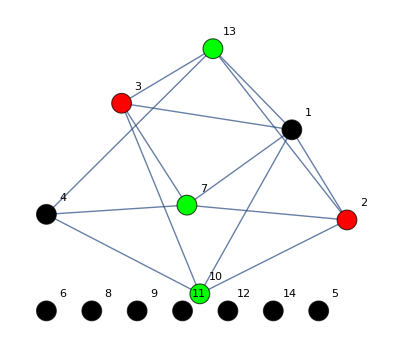

G2

NCOLORACIONES[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,0,0,1,0,1,1,0,1,1,0,1},{0,0,0,0,0,0,1,0,0,1,0,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Negro

Vértice 9, color Negro

Vértice 10, color Rojo

Vértice 11, color Negro

Vértice 12, color Negro

Vértice 13, color Rojo

Vértice 14, color Negro

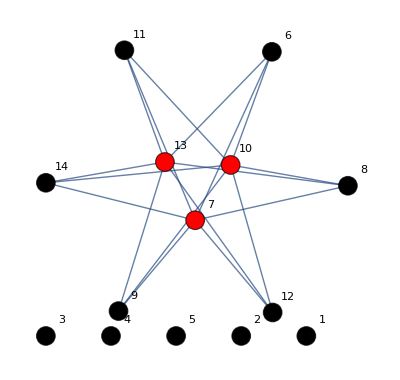

G3

NCOLORACIONES[{{0,1,1,0,0,1},{1,0,0,0,0,0},{1,0,0,0,0,0},{0,0,0,0,1,0},{0,0,0,1,0,0},{1,0,0,0,0,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Rojo

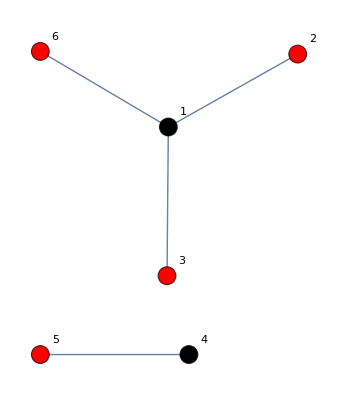

G4

NCOLORACIONES[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

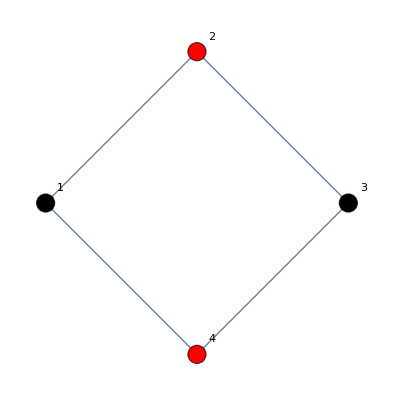

G5

NCOLORACIONES[{{0,0,0,1,1},{0,0,0,1,1},{0,0,0,1,1},{1,1,1,0,0},{1,1,1,0,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

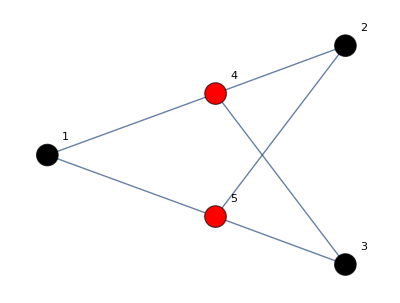

G6

NCOLORACIONES[{{0,1,0,1,0,0,0,1},{1,0,1,0,0,0,1,0},{0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,1},{0,0,1,0,1,0,1,0},{0,1,0,0,0,1,0,1},{1,0,0,0,1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

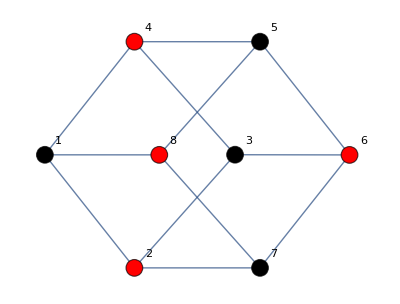

G7

NCOLORACIONES[{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}]

4

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

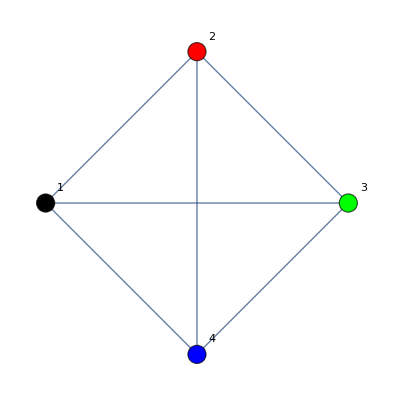

G8

NCOLORACIONES[{{0,1,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0},{0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

Vértice 9, color Negro

Vértice 10, color Rojo

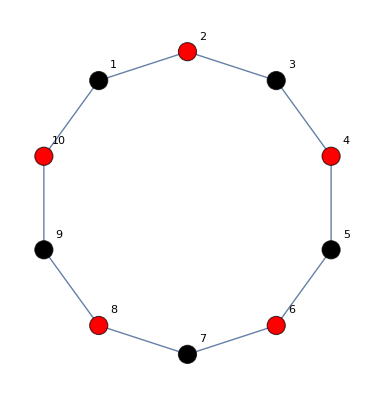

G9

NCOLORACIONES[{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}}]

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

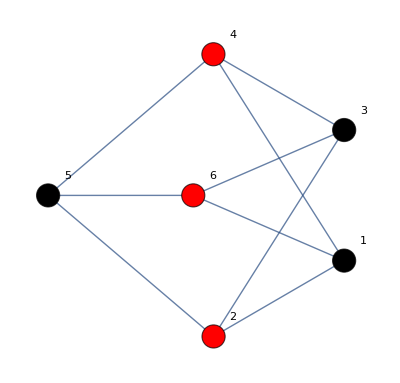

```mathematica
"G1"
AG1=MATRIZADYACENCIA[WG1,FG1];
NCOLORACIONES[AG1]
NUMEROCROMATICO[AG1]
DIBUJAR[AG1]
"G2"
AG2=MATRIZADYACENCIA[WG2,FG2];
NCOLORACIONES[AG2]
NUMEROCROMATICO[AG2]
DIBUJAR[AG2]
"G3"
AG3=MATRIZADYACENCIA[WG3,FG3];
NCOLORACIONES[AG3]
NUMEROCROMATICO[AG3]
DIBUJAR[AG3]
"G4"
AG4=MATRIZADYACENCIA[WG4,FG4];
NCOLORACIONES[AG4]
NUMEROCROMATICO[AG4]
DIBUJAR[AG4]
"G5"
AG5=MATRIZADYACENCIA[WG5,FG5];
NCOLORACIONES[AG5]
NUMEROCROMATICO[AG5]
DIBUJAR[AG5]
"G6"
AG6=MATRIZADYACENCIA[WG6,FG6];
NCOLORACIONES[AG6]
NUMEROCROMATICO[AG6]
DIBUJAR[AG6]
"G7"
AG7=MATRIZADYACENCIA[WG7,FG7];
NCOLORACIONES[AG7]
NUMEROCROMATICO[AG7]
DIBUJAR[AG7]
"G8"
AG8=MATRIZADYACENCIA[WG8,FG8];
NCOLORACIONES[AG8]
NUMEROCROMATICO[AG8]
DIBUJAR[AG8]
"G9"
AG9=MATRIZADYACENCIA[WG9,FG9];
NCOLORACIONES[AG9]
NUMEROCROMATICO[AG9]
DIBUJAR[AG9]
```

ii. Determinar si es plano

```mathematica
D3[matrizadyacencia_,i_,j_]:=Table[If[(k1==i && k2==j)||(k1==j &&k2==i),1,matrizadyacencia[[k1,k2]]],{k1,Dimensions[matrizadyacencia][[1]]},{k2,Dimensions[matrizadyacencia][[2]]}]

QUITARVERTICESGRADO210[matrizadyacencia_]:=Module[{grado2,t,W1,A,i,k,m,adya,k1,k2,k3,k4,adyacentes,j},

Nueva=matrizadyacencia;
A=Nueva.Nueva;
grado2=True;t=1;
While[grado2,
W1={};

grado2=False;
If[Dimensions[A][[1]]>2,
Do[If[A[[i,i]]==2 || A[[i,i]]==1 || A[[i,i]]==0, AppendTo[W1,i];grado2=True;],{i,Dimensions[A][[1]]}];
If[grado2,

Sort[W1];
Do[
m=W1[[Length[W1]-k+1]];

If[Dimensions[Nueva][[1]]>2,

If[A[[m,m]]==2,
adyacentes={};
Do[If[Nueva[[m,adya]]==1,AppendTo[adyacentes,adya]],{adya,Dimensions[Nueva][[1]]}];
Nueva=D3[Nueva,adyacentes[[1]],adyacentes[[2]]]
];
Nueva=Table[
If[k1≥m,k3=k1+1,k3=k1];
If[k2≥m,k4=k2+1,k4=k2];
Nueva[[k3,k4]]
,{k1,Dimensions[Nueva][[1]]-1},{k2,Dimensions[Nueva][[2]]-1}];


A=Nueva.Nueva;
];

,{k,Length[W1]}];
];

];t++;];
Nueva]

<<"Combinatorica`";
K33[W_,matrizadyacencia_]:=Module[{subconjuntos,nok33,i,k1,k2},
contiene=False;
subconjuntos=KSubsets[Complement[W,{W[[1]]}],2];
Do[
nok33=False;
A=Join[subconjuntos[[i]],{W[[1]]}];
B=Complement[W,A];
Do[
If[Sum[matrizadyacencia[[A[[k1]],B[[k2]]]],{k2,3}]<3,nok33=True;Break[];];
,{k1,3}];
If[!nok33,contiene=True;Break[];];
,{i,Length[subconjuntos]}];
contiene
]

HOMEOMORFOK5K33[matrizadyacencia_]:=Module[{Subconjuntos,i,j,cont1,matrizadyacenciaK5,Nueva},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
homeo=True;
If[Dimensions[Nueva][[1]]==6,
If[K33[{1,2,3,4,5,6},Nueva],homeo=False;]];
matrizadyacenciaK5=Table[If[i==j,0,1],{i,5},{j,5}];
If[Dimensions[Nueva][[1]]==5,If[Nueva==matrizadyacenciaK5,homeo=False;]];
homeo
]

PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

Message::name: Message name MessageName[{{0,1,1,1,1,1,1,1},{1,0,1,1,1,1,1,1},{1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,0}},usage] is not of the form symbol::name or symbol::name::language.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

G1

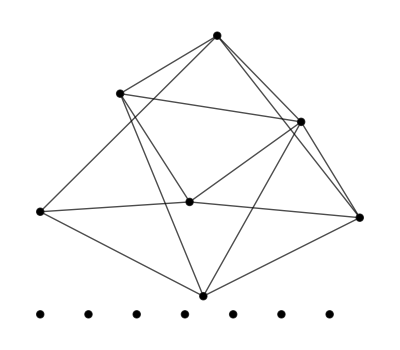

False

G2

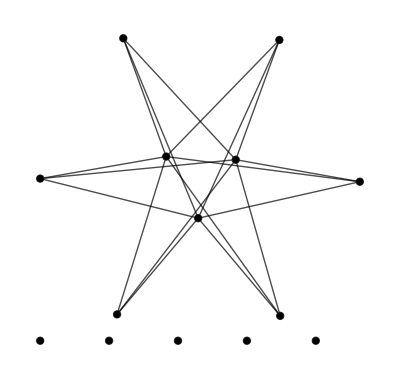

False

G3

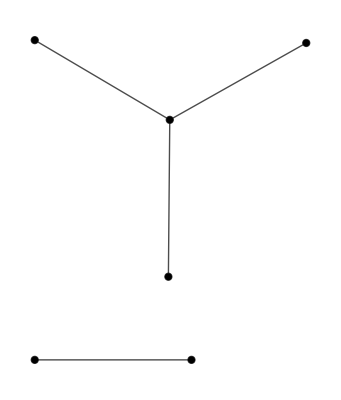

True

G4

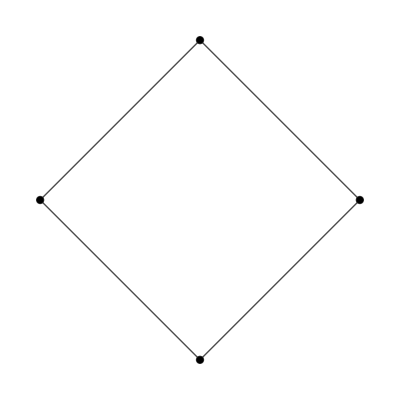

True

G5

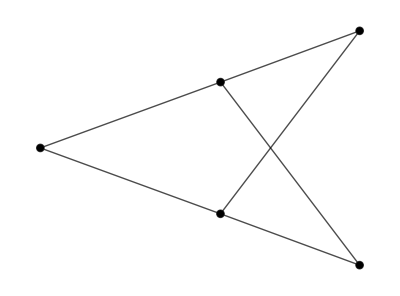

True

G6

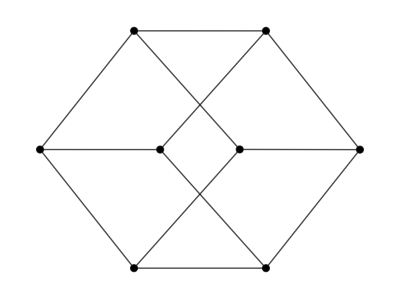

True

G7

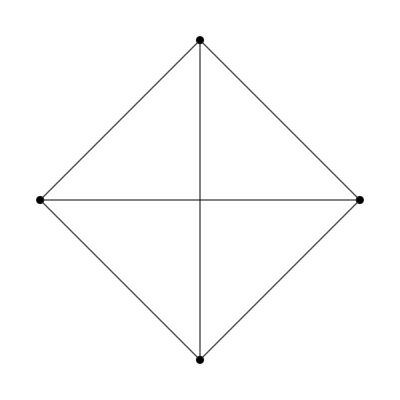

True

G1

-Graphics-

False

G8

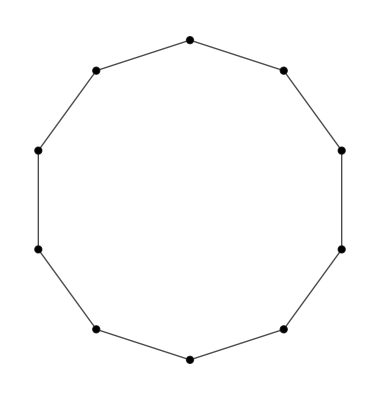

True

G9

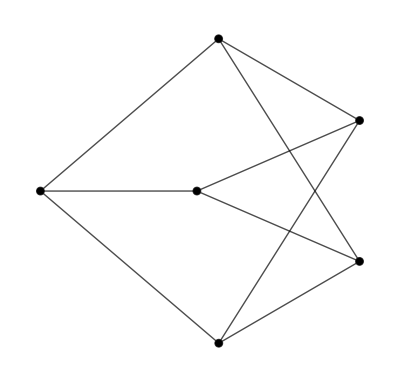

False

```mathematica
"G1"
GraphPlot[AG1,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG1]
"G2"
GraphPlot[AG2,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG2]
"G3"
GraphPlot[AG3,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG3]
"G4"
GraphPlot[AG4,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG4]
"G5"
GraphPlot[AG5,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG5]
"G6"
GraphPlot[AG6,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG6]
"G7"
GraphPlot[AG7,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG7]
"G1"
GraphPlot[AG1,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG1]
"G8"
GraphPlot[AG8,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG8]
"G9"
GraphPlot[AG9,PlotStyle->{Black,PointSize[.05]}]
PLANO[AG9]
```

iii. Comprobar si es un árbol

```mathematica
CICLOSELEMENTALES[vertice1_,longitud_,A_]:=Module[{i,ultvertice,caminos,adyacentes,caminostemp,k,j,t},
caminos={{vertice1}};
Do[
caminostemp={};
Do[
adyacentes={};

ultvertice=caminos[[k]][[i]];
Do[If[A[[ultvertice,j]]==1,AppendTo[adyacentes,j]];,{j,Dimensions[A][[1]]}];

adyacentes=Complement[adyacentes,caminos[[k]]];
If[adyacentes≠{},

Do[AppendTo[caminostemp,Append[caminos[[k]],adyacentes[[t]]]];,{t,Length[adyacentes]}];
];
,{k,Length[caminos]}];
caminos=caminostemp;
,{i,longitud-1}];
caminostemp={};
Do[If[A[[caminos[[k]][[longitud]],vertice1]]==1,AppendTo[caminostemp,Append[caminos[[k]],vertice1]];];,{k,Length[caminos]}];
caminostemp
];

BOSQUE[matrizadyacencia_]:=Module[{n,longitud,i,},
bosque=True;
n=Dimensions[matrizadyacencia][[1]];
Do[
potencia=MatrixPower[matrizadyacencia,longitud];
Do[
If[potencia[[i,i]]>0, 
If[CICLOSELEMENTALES[i,longitud,matrizadyacencia]≠{},bosque=False;Break[];];
];
,{i,n}];
If[bosque==False,Break[];];
,{longitud,3,n}];
bosque
];

CONEXO[A_]:=Module[{i,j,B},
B=Sum[MatrixPower[A,j],{j,Dimensions[A][[1]]}];
conexo=True;
Do[
Do[If[i≠j && B[[i,j]]==0,conexo=False;];
,{i,Dimensions[B][[1]]}];
,{j,Dimensions[B][[1]]}];
conexo
]

ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
COMPONENTESCONEXAS[matrizadyacencia_]:=Module[{j,B,conjunto,temp},
B=Sum[MatrixPower[matrizadyacencia,j],{j,Dimensions[matrizadyacencia][[1]]}];
componentesconexas={};
conjunto=Table[i,{i,Dimensions[B][[1]]}];
While[conjunto≠{},
temp={conjunto[[1]]};
Do[
If[B[[conjunto[[1]],conjunto[[i]]]]≠0,AppendTo[temp,conjunto[[i]]];];
,{i,2,Length[conjunto]}];
AppendTo[componentesconexas,temp];
conjunto=Complement[conjunto,temp];
];
componentesconexas
]

IND2[W1_,matrizadyacencia_]:=Module[{n,i,j},
n=Length[W1];
matrizadyacencia2=Table[0,{i,n},{j,n}];
Do[Do[
matrizadyacencia2[[i,j]]=matrizadyacencia[[W1[[i]],W1[[j]]]];
,{i,n}];
,{j,n}];
matrizadyacencia2
];

BOSQUE2[matrizadyacencia_]:=Module[{componentes,i},
bosque=True;
componentes=COMPONENTESCONEXAS[matrizadyacencia];
Do[
If[ARBOL[IND2[componentes[[i]],matrizadyacencia]]==False,bosque=False];
,{i,Length[componentes]}];
bosque]
```

```mathematica
ARBOL[AG1]
```

False

```mathematica
ARBOL[AG2]
```

False

```mathematica
ARBOL[AG3]
"G4"
ARBOL[AG4]
"G5"
ARBOL[AG5]
"G6"
ARBOL[AG6]
"G7"
ARBOL[AG7]
"G8"
ARBOL[AG8]
"G9"
ARBOL[AG9]
```

False

G4

False

G5

False

G6

False

G7

False

G8

False

G9

False